```mathematica
(*test*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\benjamin\Documents\FPII\Moessbauer\code

```mathematica
x={3.0,1.0,0.21,2.0,8.0,0.46,0.66,0.88,1.22,1.43,1.67,1.87,2.16};
names={"3.00","1.00","0.21","2.00","8.00","0.46","0.66","0.88","1.22","1.43","1.67","1.87","2.16"};
```

```mathematica
files=Flatten[Import[StringJoin["../data/background/",#,"mm.TKA"],"CSV"]]&/@names;
```

```mathematica
Dimensions[files]
```

{6,2048}

```mathematica
n=Sum[#[[90;;250]][[i]],{i,1,160}]&/@files;
r=Sort[n/600.,Greater];
data=Table[{x[[j]],Sum[files[[j]][[90;;250]][[i]],{i,1,161}]},{j,1,13}]
```

{{3.,16290},{1.,18586},{0.21,24317},{2.,16884},{8.,13786},{0.46,21964},{0.66,20335},{0.88,19388},{1.22,18089},{1.43,17644},{1.67,17280},{1.87,16971},{2.16,16971}}

```mathematica
?Sort
```

RowBox[{"Sort", "[", StyleBox["list", "TI"], "]"}] sorts the elements of StyleBox["list", "TI"] into canonical order. 
RowBox[{"Sort", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["p", "TI"]}], "]"}] sorts using the ordering function StyleBox["p", "TI"].

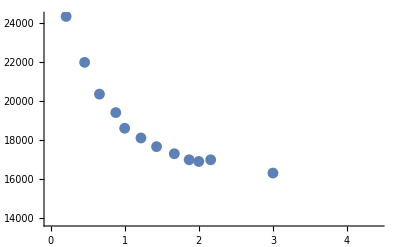

{24317,18586,16884,16290,14213,13786}

Zählrate {40.5283,30.9767,28.14,27.15,23.6883,22.9767}

```mathematica
ListPlot[data]
```